```mathematica
x0=1
x1=1.05
```

1

1.05

```mathematica
H10[x_]=(1-2(x-x0)*L10'[x0])*(L10[x])^2//Simplify
```

16000. (-1.05+x)^2 (-0.975+1. x)

```mathematica
H11[x_]=(1-2(x-x1)*L11'[x1])*(L11[x])^2//Simplify
```

-16000. (-1.+x)^2 (-1.075+1. x)

```mathematica
HH10[x_]=(x-x0)*L10[x]^2
```

400. (-1.05+x)^2 (-1+x)

```mathematica
HH11[x_]=(x-x1)*L11[x]^2
```

400. (-1.05+x) (-1+x)^2

```mathematica
f[x_]=-15999.999999999958 (-1.05+x)^2 (-1.0750000000000002+1. x)
```

-16000. (-1.05+x)^2 (-1.075+1. x)

```mathematica
f[x_]=3*x*Exp[x]-Exp[2x]
```

-ⅇ^(2 x)+3 ⅇ^x x

```mathematica
Final[x_]=f[x0]*H10[x]+f[x1]*H11[x]+f'[x0]*HH10[x]+f'[x1]*HH11[x]//Simplify
```

1.44707-7.64438 x+11.7133 x^2-4.75024 x^3

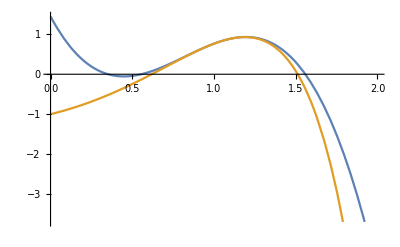

```mathematica
Plot[{Final[x],f[x]},{x,0,2}]
```

```mathematica
Final[1.05]
```

0.835431

```mathematica
f[1.05]
```

0.835431

```mathematica
(f[1.05]-Final[1.05])/Final[1.05]
```

1.77331×10^-12

```mathematica
f[1]
```

3.

```mathematica
H11[1]
```

3.

```mathematica
L10[x_]=(x-x1)/(x0-x1)
```

-20. (-1.05+x)

```mathematica
L11[x_]=(x-x0)/(x1-x0)
```

20. (-1+x)

```mathematica
g[x_]=x
```

x

```mathematica
g[1,0]
```

g[1,0]

```mathematica
a=0.0000000000
b=75.00000000001
c=0.000000000
d=.22222222222
e=-.031111111111
f=-.0064444444444
g=.0022638888889
h=-0.00091319444444
i=.00013052679158
j=-.000020223631973
```

0.

75.

0.

0.222222

-0.0311111

-0.00644444

0.00226389

-0.000913194

0.000130527

-0.0000202236

```mathematica
H[x_]=a+b*(x-0)+c*(x-0)^2+d*(x-0)^2*(x-3)+e*(x-0)^2*(x-3)^2+f*(x-0)^2*(x-3)^2*(x-5)+g*(x-0)^2*(x-3)^2*(x-5)^2+h*(x-0)^2*(x-3)^2*(x-5)^2*(x-8)+i*(x-0)^2*(x-3)^2*(x-5)^2*(x-8)^2+j*(x-0)^2*(x-3)^2*(x-5)^2*(x-8)^2*(x-13)//Simplify
```

0.+75. x+7.16191 x^2-10.0953 x^3+5.50812 x^4-1.5383 x^5+0.243041 x^6-0.0218757 x^7+0.00104059 x^8-0.0000202236 x^9

```mathematica
H[10]
```

742.503

```mathematica
H'[x]
```

75.+14.3238 x-30.2859 x^2+22.0325 x^3-7.69148 x^4+1.45825 x^5-0.15313 x^6+0.00832472 x^7-0.000182013 x^8

```mathematica
m[x_]=1-1.1*(x-0)+2.3*(x-0.5)*(x-1)
```

1+2.3 (-1+x) (-0.5+x)-1.1 x

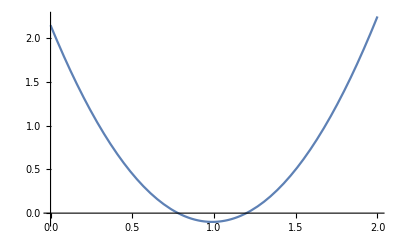

```mathematica
Plot[m[x],{x,0,2}]
```

```mathematica
m[0]
```

2.15

```mathematica
m[1]
```

-0.1